```mathematica
(*all coordinates are in blue basis unless specified otherwise*)
(*all derivatives are wrt inertial frame unless specified otherwise*)
```

```mathematica
Quit
```

```mathematica
M=1;
L=1;
Subscript[θ, z][t]=Pi (Sin[t])^2;
Subscript[θ, y][t]=Pi t;
```

```mathematica
(*define generalized speeds*)
IωB[t] = {u1[t],u2[t],u3[t]};
vCb[t]={u4[t],u5[t],u6[t]}; (*inertial velocity in B frame*)
(*green CM velocity*)
CGtoB[t] = {{1,0,0},{0, Cos[Subscript[θ, z][t]],-Sin[Subscript[θ, z][t]]},{0, Sin[Subscript[θ, z][t]],Cos[Subscript[θ, z][t]]}};
CBtoG[t] = Transpose[CGtoB[t]] ;
rCbHg = {0,-L/2,L/10};
rHgCgGreenBasis = {0,L/2,0};
rHgCg[t] = CGtoB[t].rHgCgGreenBasis;
(*two point formula: inertial velocities of two points fixed in B*)
vHg[t] = vCb[t] + Cross[IωB[t],rCbHg];
(*addition formula*)
BωG[t] ={D[Subscript[θ, z][t],t],0,0};
GωB[t] = -BωG[t];
IωG[t] =IωB[t]+BωG[t];
(*two point formula: inertial velocities of two points fixed in G*)
vCg[t] = vHg[t] + Cross[IωG[t],rHgCg[t]];
(*yellow CM velocity*)
CYtoB[t] = {{Cos[Subscript[θ, y][t]],-Sin[Subscript[θ, y][t]],0},{Sin[Subscript[θ, y][t]],Cos[Subscript[θ, y][t]],0},{0,0,1}};
CBtoY[t] = Transpose[CYtoB[t]] ;
rCbHy = {0,L/2,-L/10};
rHyCyYellowBasis = {0,-L/2,0};
rHyCy[t] = CYtoB[t].rHyCyYellowBasis;
(*two point formula*)
vHy[t] = vCb[t] + Cross[IωB[t],rCbHy];
(*addition formula*)
BωY[t] ={0,0,D[Subscript[θ, y][t],t]};
YωB[t] = -BωY[t];
IωY[t] =IωB[t]+BωY[t];
(*two point formula*)
vCy[t] = vHy[t] + Cross[IωY[t],rHyCy[t]];
```

```mathematica
(* partial velocities *)
v1B[t] = Coefficient[vCb[t],u1[t]];
v2B[t] = Coefficient[vCb[t],u2[t]];
v3B[t] = Coefficient[vCb[t],u3[t]];
ω1B[t] = Coefficient[IωB[t],u1[t]];
ω2B[t] = Coefficient[IωB[t],u2[t]];
ω3B[t] = Coefficient[IωB[t],u3[t]];
v4B[t] = Coefficient[vCb[t],u4[t]];
v5B[t] = Coefficient[vCb[t],u5[t]];
v6B[t] = Coefficient[vCb[t],u6[t]];
ω4B[t] = Coefficient[IωB[t],u4[t]];
ω5B[t] = Coefficient[IωB[t],u5[t]];
ω6B[t] = Coefficient[IωB[t],u6[t]];

v1G[t] = Coefficient[vCg[t],u1[t]];
v2G[t] = Coefficient[vCg[t],u2[t]];
v3G[t] = Coefficient[vCg[t],u3[t]];
ω1G[t] = Coefficient[IωG[t],u1[t]];
ω2G[t] = Coefficient[IωG[t],u2[t]];
ω3G[t] = Coefficient[IωG[t],u3[t]];
v4G[t] = Coefficient[vCg[t],u4[t]];
v5G[t] = Coefficient[vCg[t],u5[t]];
v6G[t] = Coefficient[vCg[t],u6[t]];
ω4G[t] = Coefficient[IωG[t],u4[t]];
ω5G[t] = Coefficient[IωG[t],u5[t]];
ω6G[t] = Coefficient[IωG[t],u6[t]];

v1Y[t] = Coefficient[vCy[t],u1[t]];
v2Y[t] = Coefficient[vCy[t],u2[t]];
v3Y[t] = Coefficient[vCy[t],u3[t]];
ω1Y[t] = Coefficient[IωY[t],u1[t]];
ω2Y[t] = Coefficient[IωY[t],u2[t]];
ω3Y[t] = Coefficient[IωY[t],u3[t]];
v4Y[t] = Coefficient[vCy[t],u4[t]];
v5Y[t] = Coefficient[vCy[t],u5[t]];
v6Y[t] = Coefficient[vCy[t],u6[t]];
ω4Y[t] = Coefficient[IωY[t],u4[t]];
ω5Y[t] = Coefficient[IωY[t],u5[t]];
ω6Y[t] = Coefficient[IωY[t],u6[t]];
```

```mathematica
(* compute inertial angular accelerations *)
αB[t] = D[IωB[t],t]; (* IdIwB = BdIwB *)
αGGreenBasis[t]=D[CBtoG[t].IωG[t],t];
αG[t] = CGtoB[t].αGGreenBasis[t];
αYYellowBasis[t]=D[CBtoY[t].IωY[t],t];
αY[t] = CYtoB[t].αYYellowBasis[t];
(*inertia tensors*)
Mg = M/4;
My = M/4;
ICb = {{1/12 M(L^2+(L/5)^2),0,0},{0,1/12 M(2(L/5)^2),0},{0,0,1/12 M(L^2+(L/5)^2)}};
ICg = {{1/12Mg L^2,0,0},{0,0,0},{0,0,1/12 Mg L^2}};
ICy = {{1/12My L^2,0,0},{0,0,0},{0,0,1/12 My L^2}};
(* compute torques in their respective body frames *)
TstarB[t] = -ICb.αB[t] - Cross[IωB[t],ICb.IωB[t]];
TstarGGreenBasis[t] = -ICg.αGGreenBasis[t] - Cross[CBtoG[t].IωG[t],ICg.(CBtoG[t].IωG[t])];
TstarYYellowBasis[t] = -ICy.αYYellowBasis[t] - Cross[CBtoY[t].IωY[t],ICy.(CBtoY[t].IωY[t])];
(* compute inertial accelerations using transport theorem and two points formula*)
aCb[t] = D[vCb[t],t]+Cross[IωB[t],vCb[t]];
aHg[t] = aCb[t] + Cross[IωB[t],Cross[IωB[t],rCbHg]] + Cross[αB[t],rCbHg];
aCg[t] =aHg[t] + Cross[BωG[t],Cross[BωG[t],rHgCg[t]]] + Cross[αG[t],rHgCg[t]];
aHy[t] = aCb[t] + Cross[IωB[t],Cross[IωB[t],rCbHy]] + Cross[αB[t],rCbHy];
aCy[t] =aHy[t] + Cross[BωY[t],Cross[BωY[t],rHyCy[t]]] + Cross[αY[t],rHyCy[t]];
(* compute resultant forces in B frame *)
RstarB[t]=-M*aCb[t];
RstarG[t]=-Mg*aCg[t];
RstarY[t]=-My*aCy[t];
F1starB[t] =Simplify[(v1B[t].RstarB[t]+ ω1B[t].TstarB[t])+(v1G[t].RstarG[t]+ (CBtoG[t].ω1G[t]).TstarGGreenBasis[t])+(v1Y[t].RstarY[t]+ (CBtoY[t].ω1Y[t]).TstarYYellowBasis[t])];
F2starB[t] = Simplify[(v2B[t].RstarB[t]+ ω2B[t].TstarB[t])+(v2G[t].RstarG[t]+ CBtoG[t].ω2G[t].TstarGGreenBasis[t])+(v2Y[t].RstarY[t]+ CBtoY[t].ω2Y[t].TstarYYellowBasis[t])];
F3starB[t] = Simplify[(v3B[t].RstarB[t]+ ω3B[t].TstarB[t])+(v3G[t].RstarG[t]+ CBtoG[t].ω3G[t].TstarGGreenBasis[t])+(v3Y[t].RstarY[t]+CBtoY[t]. ω3Y[t].TstarYYellowBasis[t])];
F4starB[t] = Simplify[(v4B[t].RstarB[t]+ ω4B[t].TstarB[t])+(v4G[t].RstarG[t]+ CBtoG[t].ω4G[t].TstarGGreenBasis[t])+(v4Y[t].RstarY[t]+ CBtoY[t].ω4Y[t].TstarYYellowBasis[t])];
F5starB[t] = Simplify[(v5B[t].RstarB[t]+ ω5B[t].TstarB[t])+(v5G[t].RstarG[t]+ CBtoG[t].ω5G[t].TstarGGreenBasis[t])+(v5Y[t].RstarY[t]+ CBtoY[t].ω5Y[t].TstarYYellowBasis[t])];
F6starB[t] = Simplify[(v6B[t].RstarB[t]+ ω6B[t].TstarB[t])+(v6G[t].RstarG[t]+ CBtoG[t].ω6G[t].TstarGGreenBasis[t])+(v6Y[t].RstarY[t]+ CBtoY[t].ω6Y[t].TstarYYellowBasis[t])];
```

```mathematica
Eq1 = F1starB[t];
Eq2 = F2starB[t];
Eq3 = F3starB[t];
Eq4 = F4starB[t];
Eq5 = F5starB[t];
Eq6 = F6starB[t];
(*mySol=NDSolve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0,Eq5==0,Eq6==0,u1[0]==0,u2[0]==0,u3[0]==0,u4[0]==0,u5[0]==0,u6[0]==0},{u1,u2,u3,u4,u5,u6},{t,0,1},Method->{"EquationSimplification"->"Residual"}][[1]];*)
```

```mathematica
rOCbInertialBasis[t] = {q4[t],q5[t],q6[t]};
vCbInertialBasis[t]=D[rOCbInertialBasis[t],t];
(*direction cosine matrix*)
CBtoI[t] = {{Cos[q2[t]]Cos[q3[t]],-Cos[q2[t]]Sin[q3[t]],Sin[q2[t]]},{Sin[q1[t]]Sin[q2[t]]Cos[q3[t]]+Sin[q3[t]]Cos[q1[t]],-Sin[q1[t]]Sin[q2[t]]Sin[q3[t]]+Cos[q3[t]]Cos[q1[t]],-Sin[q1[t]]Cos[q2[t]]},{-Cos[q1[t]]Sin[q2[t]]Cos[q3[t]]+Sin[q3[t]]Sin[q1[t]],Cos[q1[t]]Sin[q2[t]]Sin[q3[t]]+Cos[q3[t]]Sin[q1[t]],Cos[q1[t]]Cos[q2[t]]}};
CItoB[t]=Transpose[CBtoI[t]];
(*Cb is center of mass of B*)
KDEvCb[t] = CItoB[t].vCbInertialBasis[t];
(*M matrix*)
CMixedtoB[t] = {{Cos[q2[t]]Cos[q3[t]],Sin[q3[t]],0},{-Cos[q2[t]]Sin[q3[t]],Cos[q3[t]],0},{Sin[q2[t]],0,1}};
KDEIωB[t] = Simplify[CMixedtoB[t].D[{q1[t],q2[t],q3[t]},t]];
```

```mathematica
KDESol=NDSolve[{u1[t]==KDEIωB[t][[1]],u2[t]==KDEIωB[t][[2]],u3[t]==KDEIωB[t][[3]],u4[t]==KDEvCb[t][[1]],u5[t]==KDEvCb[t][[2]],u6[t]==KDEvCb[t][[3]],q1[0]==0,q2[0]==0,q3[0]==0,q4[0]==0,q5[0]==0,q6[0]==0,Eq1==0,Eq2==0,Eq3==0,Eq4==0,Eq5==0,Eq6==0,u1[0]==0,u2[0]==0,u3[0]==0,u4[0]==0,u5[0]==0,u6[0]==0},{q1,q2,q3,q4,q5,q6,u1,u2,u3,u4,u5,u6},{t,0,1},Method->{"EquationSimplification"->"Residual"}];
```

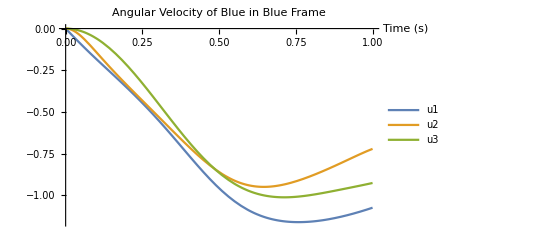

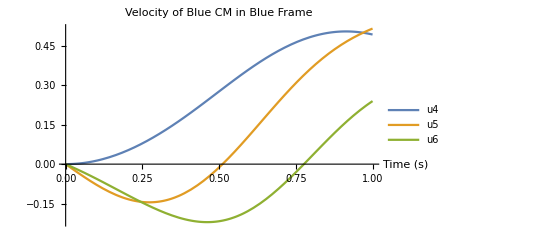

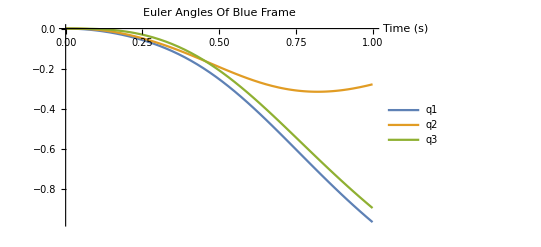

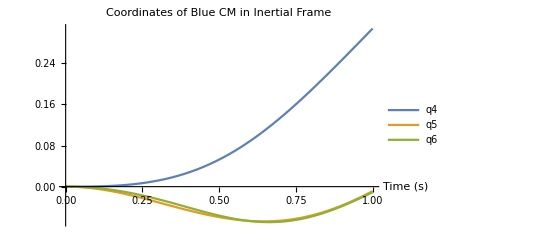

```mathematica
Plot[Evaluate[{u1[t],u2[t],u3[t]}/. KDESol],{t,0,1},PlotRange->All,
PlotLegends->{"u1","u2","u3"},AxesLabel->{"Time (s)"},PlotLabel->"Angular Velocity of Blue in Blue Frame"]
Plot[Evaluate[{u4[t],u5[t],u6[t]}/. KDESol],{t,0,1},PlotRange->All,
PlotLegends->{"u4","u5","u6"},AxesLabel->{"Time (s)"},PlotLabel->"Velocity of Blue CM in Blue Frame"]
Plot[Evaluate[{q1[t],q2[t],q3[t]}/. KDESol],{t,0,1},PlotRange->All,
PlotLegends->{"q1","q2","q3"},AxesLabel->{"Time (s)"},PlotLabel->"Euler Angles Of Blue Frame"]
Plot[Evaluate[{q4[t],q5[t],q6[t]}/. KDESol],{t,0,1},PlotRange->All,
PlotLegends->{"q4","q5","q6"},AxesLabel->{"Time (s)"},PlotLabel->"Coordinates of Blue CM in Inertial Frame"]
```

```mathematica
(*Validation: the center of mass should be constant in inertial frame, and the magnitude of total angular momentum should be conserved*)
rOCb[t] = CItoB[t]. rOCbInertialBasis[t];
rOCg[t] = rOCb[t] + rCbHg + rHgCg[t];
rOCy[t] = rOCb[t] + rCbHy + rHyCy[t];
CMInertialBasis[t] = Simplify[CBtoI[t].(M rOCb[t]+Mg rOCg[t]+My rOCy[t])/(M+Mg+My)];
LO[t] = Simplify[ICb.IωB[t]+ Cross[rOCb[t],M vCb[t]]+CGtoB[t].(ICg.CBtoG[t].IωG[t])+Cross[rOCg[t],Mg vCg[t]] + CYtoB[t].(ICy.CBtoY[t].IωY[t])+Cross[rOCy[t],My vCy[t]]];
```

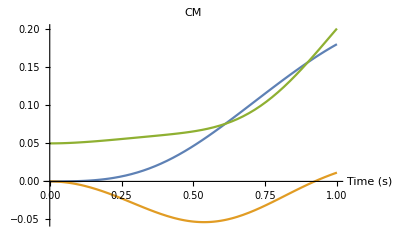

```mathematica
Plot[Evaluate[CM[t]/. KDESol],{t,0,1},PlotRange->All,AxesLabel->{"Time (s)"},PlotLabel->"CM"]
```

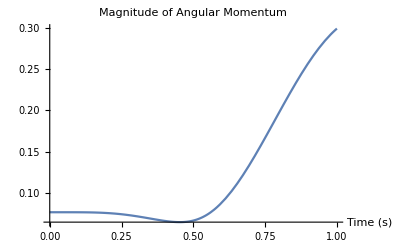

```mathematica
Plot[Evaluate[Norm[LO[t]]/. KDESol],{t,0,1},PlotRange->All,AxesLabel->{"Time (s)"},PlotLabel->"Magnitude of Angular Momentum"]
```